```mathematica
Clear["Global`*"]
```

```mathematica
M:=0.00227958
p:=4
μ:=5
ϕini:=1.08556
ϕend:=4.41822
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,0,2.12 10^7}];
asr[t_]:=(a/.First[sol])[t]
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
sol1=NDSolve[{ϕ''[t]+ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (1/2 ϕ'[t]^2+V[t])], 
ϕ[0]==ϕsr[0],ϕ'[0]==ϕsrp[0],a[0]==asr[0]},{ϕ,a},
{t,0,2.12 10^7}];
aex[t_]:=(a/.First[sol1])[t]
aexpp[t_]=D[aex[t],{t,2}];
ϕex[t_]:=(ϕ/.First[sol1])[t]
fun[t_]:=aexpp[t]/aex[t]
tend = FindRoot[ϕex[t] == ϕend, {t, 2.1 10^7}]
```

{t→2.08681×10^7}

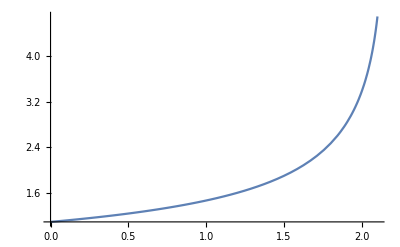

```mathematica
Plot[ϕex[t],{t,0,2.10 10^7},PlotRange->All]
```

```mathematica
Plot[aex[t],{t,0,2.12 10^7}]
```

-Graphics-

```mathematica
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\hilltop_aex _mu=5_N=60_v2.dat",FormatType->OutputForm];
For[i=0,i<42200,i++,Write[strm,k=CForm[500 i],"    ",CForm[Re[aex[500 i]]]]]
Close[strm];
```

```mathematica
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\hilltop_phiex _mu=5_N=60_v2.dat",FormatType->OutputForm];
For[i=0,i<42200,i++,Write[strm,k=CForm[500 i],"    ",CForm[Re[ϕex[500 i]]]]]
Close[strm];
```

## Fitting

```mathematica
M:=0.00227958
p:=4
μ:=5
ϕini:=1.08556
ϕend:=4.41822
```

```mathematica
adat = Import["C:\\Users\\RAUL\\Downloads\\hilltop_aex _mu=5_N=60_v2.dat"];
ϕdat = Import["C:\\Users\\RAUL\\Downloads\\hilltop_phiex _mu=5_N=60_v2.dat"];
```

```mathematica
alogdat =Transpose[{Transpose[adat][[1]],Log[Transpose[adat][[2]]]}];
ϕlogdat =Transpose[{Transpose[ϕdat][[1]],Log[Transpose[ϕdat][[2]]]}];
```

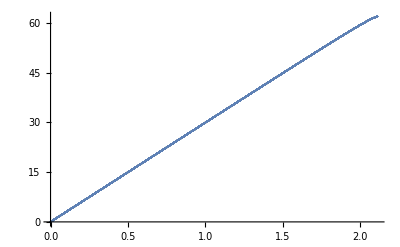

```mathematica
ListPlot[alogdat]
```

```mathematica
alogfit2 =NonlinearModelFit[alogdat,,{d},t]
alogfit2["RSquared"]
Normal[alogfit2]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[ⅇ^(0.999995 t)]

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

-1.75268912029895×10^18326264

ⅇ^(0.999995 t)

```mathematica
alogfit =NonlinearModelFit[alogdat[[30000;;42200]], b t^15+c t^14 + d t^13 +e t^12 +f t^11 +g t^10 + h t^9 + i t^8 + j t^7+ k t^6 + l t^5 + m t^4 + n t^3+ o t^2 + q t^1  ,{b, c,d,e,f,g,h, i,j,k,l,m,n,o,q},t]
alogfit["RSquared"]
Normal[alogfit]
```

FittedModel[-0.0748299 t+3.05162×10^-8 t^2-4.89094×10^-15 t^3+«12»+1.03167×10^-80 t^12-7.57342×10^-88 t^13+1.80303×10^-95 t^14-1.55581×10^-103 t^15]

1.

-0.0748299 t+3.05162×10^-8 t^2-4.89094×10^-15 t^3+3.51645×10^-22 t^4-5.29252×10^-30 t^5-6.98268×10^-37 t^6+2.09025×10^-44 t^7+1.65308×10^-51 t^8-5.27164×10^-59 t^9-4.32057×10^-66 t^10+1.52737×10^-73 t^11+1.03167×10^-80 t^12-7.57342×10^-88 t^13+1.80303×10^-95 t^14-1.55581×10^-103 t^15

```mathematica
ϕfit =NonlinearModelFit[ϕlogdat, b t^15+c t^14 + d t^13 +e t^12 +f t^11 +g t^10 + h t^9 + i t^8 + j t^7+ k t^6 + l t^5 + m t^4 + n t^3+ o t^2 + q t^1 + r  ,{b, c,d,e,f,g,h, i,j,k,l,m,n,o,q,r},t]
ϕfit["RSquared"]
Normal[ϕfit]
```

FittedModel[0.0816697+2.78354×10^-8 t-1.55899×10^-14 t^2+2.1156×10^-20 t^3-1.51942×10^-26 t^4+«12»+2.21841×10^-89 t^13-3.26606×10^-97 t^14+2.1651×10^-105 t^15]

1.

0.0816697+2.78354×10^-8 t-1.55899×10^-14 t^2+2.1156×10^-20 t^3-1.51942×10^-26 t^4+6.73116×10^-33 t^5-1.97293×10^-39 t^6+3.99887×10^-46 t^7-5.75772×10^-53 t^8+5.97216×10^-60 t^9-4.47427×10^-67 t^10+2.39816×10^-74 t^11-8.9638×10^-82 t^12+2.21841×10^-89 t^13-3.26606×10^-97 t^14+2.1651×10^-105 t^15

```mathematica
nlmϕ = NonlinearModelFit[ϕdat, b t^15+c t^14 + d t^13 +e t^12 +f t^11 +g t^10 + h t^9 + i t^8 + j t^7+ k t^6 + l t^5 + m t^4 + n t^3+ o t^2 + q t^1 + r  ,{b, c,d,e,f,g,h, i,j,k,l,m,n,o,q,r},t];(*nlma = NonlinearModelFit[adat, b t^15+c t^14 + d t^13 +e t^12 +f t^11 +g t^10 + h t^9 + i t^8 + j t^7+ k t^6 + l t^5 + m t^4 + n t^3+ o t^2 + q t^1 + r  ,{b, c,d,e,f,g,h, i,j,k,l,m,n,o,q,r},t];*)
```

```mathematica
afit = FindFormula[alogdat,t]
```

$Aborted

```mathematica
ϕfitfur = FindFormula[ϕlogdat,t]
```

0.151643+5.13765×10^-9 t+1.7717×10^-15 t^2

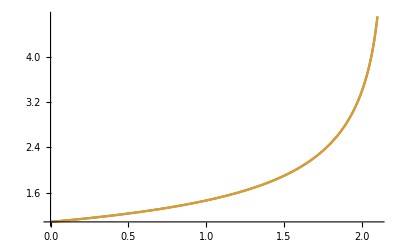

```mathematica
Plot[{Exp[0.08166965863029756+2.7835447954507715*^-8 t-1.558991925581659*^-14 t^2+2.1156027049150633*^-20 t^3-1.519424199216129*^-26 t^4+6.731158213402628*^-33 t^5-1.9729253431577412*^-39 t^6+3.998872945152843*^-46 t^7-5.757720996483203*^-53 t^8+5.97216330563661*^-60 t^9-4.474269137484226*^-67 t^10+2.3981637409620746*^-74 t^11-8.963802691295585*^-82 t^12+2.2184097478685533*^-89 t^13-3.266064565727318*^-97 t^14+2.1650995261705003*^-105 t^15],ϕex[t]},{t,0,2.1×10^7},PlotRange->All]
```

```mathematica
Plot[{Exp[2.986479697409484*^-6 t+4.1712800474450736*^-14 t^2-6.199424035321218*^-20 t^3+4.7576346292946137*^-26 t^4-2.1971313830767173*^-32 t^5+6.627796769240853*^-39 t^6-1.3720215586813769*^-45 t^7+2.0076798283529503*^-52 t^8-2.109271855399865*^-59 t^9+1.5967493128616072*^-66 t^10-8.632511422270675*^-74 t^11+3.250196420448566*^-81 t^12-8.094003894962936*^-89 t^13+1.1980911113304061*^-96 t^14-7.979845089458832*^-105 t^15],aex[t]},{t,0,2.1 10^7},PlotRange->All]
```

-Graphics-

```mathematica
Show[{ListLinePlot[adat,PlotStyle->Dashed,PlotRange->All],Plot[Exp[2.986479697409484*^-6 t+4.1712800474450736*^-14 t^2-6.199424035321218*^-20 t^3+4.7576346292946137*^-26 t^4-2.1971313830767173*^-32 t^5+6.627796769240853*^-39 t^6-1.3720215586813769*^-45 t^7+2.0076798283529503*^-52 t^8-2.109271855399865*^-59 t^9+1.5967493128616072*^-66 t^10-8.632511422270675*^-74 t^11+3.250196420448566*^-81 t^12-8.094003894962936*^-89 t^13+1.1980911113304061*^-96 t^14-7.979845089458832*^-105 t^15],{t,0,2.1 10^7},PlotRange->All]}]
```

-Graphics-

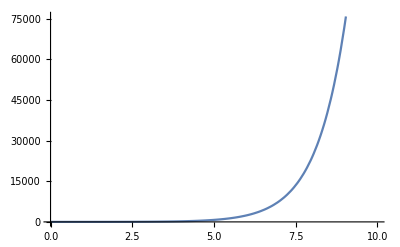

```mathematica
Plot[Exp[t +Log[t]],{t,0,10}]
```

```mathematica
ϕ[t_]:= Exp[0.08166965863029756+2.7835447954507715*^-8 t-1.558991925581659*^-14 t^2+2.1156027049150633*^-20 t^3-1.519424199216129*^-26 t^4+6.731158213402628*^-33 t^5-1.9729253431577412*^-39 t^6+3.998872945152843*^-46 t^7-5.757720996483203*^-53 t^8+5.97216330563661*^-60 t^9-4.474269137484226*^-67 t^10+2.3981637409620746*^-74 t^11-8.963802691295585*^-82 t^12+2.2184097478685533*^-89 t^13-3.266064565727318*^-97 t^14+2.1650995261705003*^-105 t^15];
pϕ[t_]= D[ϕ[t],t];
ppϕ[t_] = D[ϕ[t],{t,2}];
pppϕ[t_] = D[ϕ[t],{t,3}];
a[t_]:=Exp[2.986479697409484*^-6 t+4.1712800474450736*^-14 t^2-6.199424035321218*^-20 t^3+4.7576346292946137*^-26 t^4-2.1971313830767173*^-32 t^5+6.627796769240853*^-39 t^6-1.3720215586813769*^-45 t^7+2.0076798283529503*^-52 t^8-2.109271855399865*^-59 t^9+1.5967493128616072*^-66 t^10-8.632511422270675*^-74 t^11+3.250196420448566*^-81 t^12-8.094003894962936*^-89 t^13+1.1980911113304061*^-96 t^14-7.979845089458832*^-105 t^15]
pa[t_]= D[a[t],t];
ppa[t_] = D[a[t],{t,2}];
pppa[t_] = D[a[t],{t,3}];
```

```mathematica
tend = t/.FindRoot[ϕ[t] ==ϕend,{t, 10^7}];
```

```mathematica
tend
```

2.08659×10^7

```mathematica
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},MaxStepSize->100,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.0015
{nS[0.002],r[0.002]}
```

{0.968005,0.000699333}